```mathematica
δ1=Assuming[k∈Integers,(Series[x Cos[x],{x,(2k+1)π/2,1}]//Normal)/.x->((2k+1)π/2+δ)//FullSimplify]
δ2=Assuming[k∈Integers,(Series[Sin[x],{x,(2k+1)π/2,1}]//Normal)/.x->((2k+1)π/2+δ)//FullSimplify]
Solve[δ1==δ2,δ]//FullSimplify
```

-1/2 (-1)^k (1+2 k) π δ

(-1)^k

{{δ→-2/(π+2 k π)}}

Power::infy: Infinite expression 1/0 encountered.

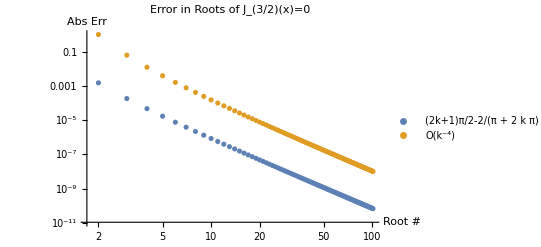

```mathematica
rootK[k_]:=FindRoot[BesselJ[3/2,x]==0,{x,(2k+1)π/2}];
asymptK0[k_]=(2k+1)π/2;
asymptK1[k_]=(2k+1)π/2-2/(π+2k π);
errK0[k_]:=Abs[(x/.rootK[k])-asymptK0[k]]/(x/.rootK[k]);
errK1[k_]:=Abs[(x/.rootK[k])-asymptK1[k]]/(x/.rootK[k]);
dat0=errK0/@Table[k,{k,0,100}];
dat1=errK1/@Table[k,{k,0,100}];
ListLogLogPlot[{dat1,Table[1/k^4,{k,0,100}]},
PlotLegends->{"(2k+1)π/2-2/(π + 2  k π)","O(k^-4)"},
PlotLabel->Style["Error in Roots of J_(3/2)(x)=0",15],
AxesLabel->{"Root #","Abs Err"}]
```

```mathematica
D[BesselJ[3/2,x], x]//FullSimplify
```

(3 x Cos[x]+(-3+2 x^2) Sin[x])/(√(2 π) x^(5/2))

```mathematica
sol1=Assuming[k∈Integers,Normal[Series[(3-2 x^2)Sin[x],{x,k π,1}]]/.x->(k π+δ)//FullSimplify]
sol2=Assuming[k∈Integers,Normal[Series[3 x Cos[x],{x,k π,1}]]/.x->(k π+δ)//FullSimplify]
Solve[sol1==sol2,δ]
```

(-1)^k (3-2 k^2 π^2) δ

3 (-1)^k (k π+δ)

{{δ→-3/(2 k π)}}

Power::infy: Infinite expression 1/(√0.) encountered.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {0.}.

ReplaceAll::reps: {FindRoot[∂_x BesselJ[3/2,x]==0,{x,0 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {0.}.

ReplaceAll::reps: {FindRoot[∂_x BesselJ[3/2,x]==0,{x,0 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_x BesselJ[3/2,x]==0,{x,0 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Power::infy: Infinite expression 1/(√0.) encountered.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {0.}.

ReplaceAll::reps: {FindRoot[∂_x BesselJ[3/2,x]==0,{x,0 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {0.}.

ReplaceAll::reps: {FindRoot[∂_x BesselJ[3/2,x]==0,{x,0 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_x BesselJ[3/2,x]==0,{x,0 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

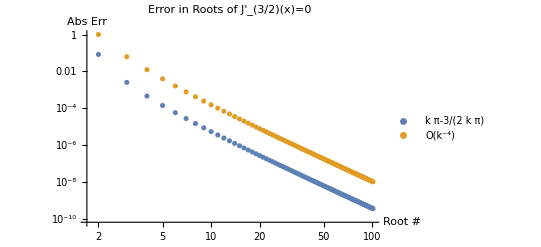

```mathematica
rootK[k_]:=FindRoot[D[BesselJ[3/2,x], x]==0,{x,k π}];
asymptK[k_]=k π-3/(2k π);
errK[k_]:=Abs[(x/.rootK[k])-asymptK[k]]/(x/.rootK[k]);
dat=errK/@Table[k,{k,0,100}];
ListLogLogPlot[{dat,Table[1/k^4,{k,0,100}]},
PlotLegends->{"k π-3/(2  k π)","O(k^-4)"},
PlotLabel->Style["Error in Roots of J'_(3/2)(x)=0",15],
AxesLabel->{"Root #","Abs Err"}]
```

```mathematica
Asymptotic[Log[Cot[ϵ]],ϵ->0]
Asymptotic[Sinh[ϵ],ϵ->∞]
Asymptotic[Coth[ϵ],ϵ->∞]
Asymptotic[ϵ^(3/4)/(1-Cos[ϵ]),ϵ->0]
Asymptotic[Log[1+Log[(1+2ϵ)/ϵ]],ϵ->0]
```

Log[1/ϵ]

ⅇ^ϵ/2

1

2/ϵ^(5/4)

Log[1+Log[1/ϵ]]

```mathematica
lim_(ϵ->0^+) Log[1+Log[1/ϵ]]/Log[Log[1/ϵ]]
```

1

True

True

True

«1 more identical outputs»

General::munfl: Exp[-830382.] is too small to represent as a normalized machine number; precision may be lost.

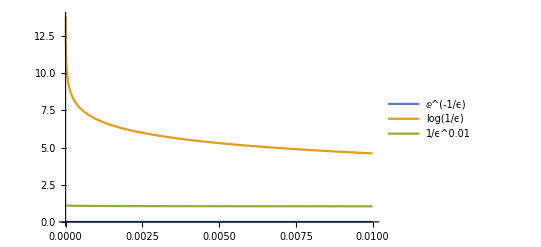

```mathematica
AsymptoticLess[ⅇ^(-1/ϵ),Log[1/ϵ],ϵ->0,Direction->"FromAbove"]
AsymptoticLess[Log[1/ϵ],ϵ^-0.01,ϵ->0,Direction->"FromAbove"]
AsymptoticLess[ϵ^-0.01,Cot[ϵ],ϵ->0,Direction->"FromAbove"]
AsymptoticLess[Cot[ϵ],Sinh[1/ϵ],ϵ->0,Direction->"FromAbove"]
Plot[{ⅇ^(-1/ϵ),Log[1/ϵ],ϵ^-0.01},{ϵ,0.000001,.01},PlotLegends->"Expressions"]
```

General::munfl: Exp[-489510.] is too small to represent as a normalized machine number; precision may be lost.

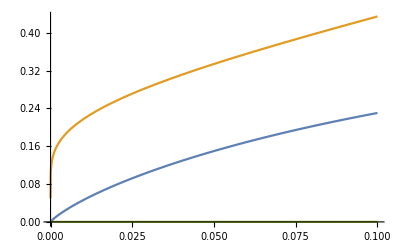

```mathematica
Plot[{Abs[ϵ Log[ϵ]],1/Log[1/ϵ],ⅇ^(-1/ϵ)},{ϵ,0,.1}]
```

```mathematica
AsymptoticGreater[Sinh[1/ϵ],Cot[ϵ],ϵ->0,Direction->"FromAbove"]
AsymptoticGreater[Cot[ϵ],Sin[ϵ]/ϵ^(3/4),ϵ->0,Direction->"FromAbove"]
AsymptoticGreater[Tanh[1/ϵ],Sin[ϵ]/ϵ^(3/4),ϵ->0,Direction->"FromAbove"]
AsymptoticGreater[Sin[ϵ]/ϵ^(3/4),Log[1+ϵ],ϵ->0,Direction->"FromAbove"]
AsymptoticGreater[1/Log[1/ϵ],Log[1+ϵ],ϵ->0,Direction->"FromAbove"]
AsymptoticGreater[ϵ Log[ϵ],Log[1+ϵ],ϵ->0,Direction->"FromAbove"]
AsymptoticGreater[Log[1+ϵ],ⅇ^(-1/ϵ),ϵ->0,Direction->"FromAbove"]
```

True

True

True

«4 more identical outputs»

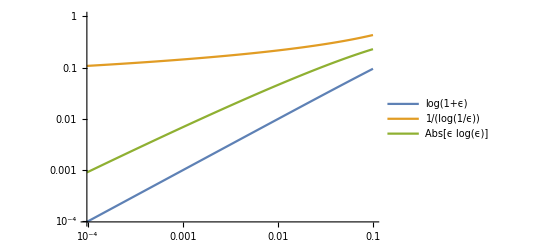

```mathematica
LogLogPlot[{Log[1+ϵ],1/Log[1/ϵ],Abs[ϵ Log[ϵ]]},{ϵ,0,0.1},PlotLegends->"Expressions"]
```

```mathematica
Asymptotic[ArcSech[ϵ],ϵ->0]
```

-Log[ϵ]

```mathematica
ArcSech[x]//TrigToExp
```

Log[√(-1+1/x) √(1+1/x)+1/x]

```mathematica
Asymptotic[√(ϵ(1-ϵ)),ϵ->0]
```

√ϵ

```mathematica
Asymptotic[ϵ^(1/2)/(1-Cos[ϵ]),ϵ->0]
```

2/ϵ^(3/2)

```mathematica
Asymptotic[ⅇ^(-Cosh[ϵ]),ϵ->∞]
```

ⅇ^(-Cosh[ϵ])

```mathematica
Asymptotic[Log[1+Log[(1+2ϵ)/ϵ]/(1-2ϵ)],ϵ->0]
Asymptotic[Log[1+Log[1+2ϵ]/(ϵ(1-2ϵ))],ϵ->0]
```

Log[1+Log[1/ϵ]]

Log[3]

```mathematica
AsymptoticEquivalent[Log[1+Log[1/ϵ]],Log[Log[1/ϵ]],ϵ->0,Direction->"FromAbove"]
```

True

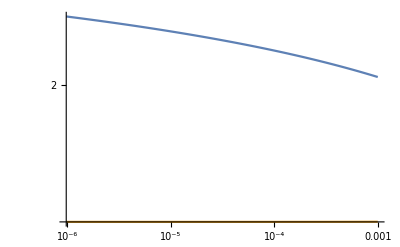

```mathematica
LogLogPlot[{Log[1+Log[(1+2ϵ)/ϵ]/(1-2ϵ)],Log[1+Log[1+2ϵ]/(ϵ(1-2ϵ))]},{ϵ,0,0.001},PlotRange->All]
```

```mathematica
AsymptoticGreater[ϵ^(1/2)/(1-Cos[ϵ]),ArcSech[ϵ],ϵ->0,Direction->"FromAbove"]
AsymptoticGreater[ArcSech[ϵ],Log[1+Log[(1+2ϵ)/ϵ]/(1-2ϵ)],ϵ->0,Direction->"FromAbove"]
AsymptoticGreater[Log[1+Log[(1+2ϵ)/ϵ]/(1-2ϵ)],Log[1+Log[1+2ϵ]/(ϵ(1-2ϵ))],ϵ->0,Direction->"FromAbove"]

AsymptoticGreater[Log[1+Log[1+2ϵ]/(ϵ(1-2ϵ))],√(ϵ(1-ϵ)),ϵ->0,Direction->"FromAbove"]

AsymptoticGreater[√(ϵ(1-ϵ)),Log[1+ϵ],ϵ->0,Direction->"FromAbove"]

AsymptoticGreater[Log[1+ϵ],(1-Cos[ϵ])/(1+Cos[ϵ]),ϵ->0,Direction->"FromAbove"]

AsymptoticGreater[(1-Cos[ϵ])/(1+Cos[ϵ]),ⅇ^(-Cosh[1/ϵ]),ϵ->0,Direction->"FromAbove"]
```

True

True

True

«4 more identical outputs»

```mathematica
Assuming[k∈Integers&&k>0&&n∈Integers&&n>0,(∫_0^π A^{1,2,3}Sin[k x]^({1,2,3}+1)ⅆx)/(∫_0^π A Sin[k x]^2 ⅆx)//FullSimplify]
```

{1,-(4 (-1+(-1)^k) A)/(3 k π),(3 A^2)/4}